```mathematica
<<MaTeX``
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
pwd="/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu";
```

# Gráficas para proyecto (y un poco más)

Amado Cabrera, Denilson Mendoza y Mariana Pérez

## Importando datos

### Solución exacta de la EDO

```mathematica
edo=y/.DSolve[{y'[x]==0.16y[x],y[0]==367},y,x][[1]]
```

Function[{x},367. ⅇ^(0.16 x)]

### Método de Euler

```mathematica
TableForm[#,TableHeadings->{None,{"i","xi","yi"}}]&@((euler=Import[pwd<>"/data/data-euler.csv","Data"][[2;;]])[[1;;5]]~Join~{{"...","...","..."}})
```

i | xi | yi
0 | 0. | 367.
1 | 0.2 | 378.744000000000028
2 | 0.4 | 390.863808000000006
3 | 0.6 | 403.371449856000027
4 | 0.8 | 416.27933625139201
... | ... | ...

El error después de 100 iteraciones viene dado por

```mathematica
(eulerEr=Abs[#[[;;,3]]-edo/@#[[;;,2]]]&@euler)//Last
```

440.244

```mathematica
Export[pwd<>"/data/data-eulerEr.csv",(eulerᵀ~Join~{eulerEr})ᵀ,"Table"]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/data/data-eulerEr.csv

### Método de Taylor

```mathematica
TableForm[#,TableHeadings->{None,{"i","xi","yi"}}]&@((taylor=Import[pwd<>"/data/data-taylor.csv","Data"][[2;;]])[[1;;5]]~Join~{{"...","...","..."}})
```

i | xi | yi
0 | 0. | 367.
1 | 0.2 | 378.933924343807973
2 | 0.4 | 391.255910132421775
3 | 0.6 | 403.978576155822509
4 | 0.8 | 417.11495153555785
... | ... | ...

El error después de 100 iteraciones viene dado por

```mathematica
(taylorEr=Abs[#[[;;,3]]-edo/@#[[;;,2]]]&@taylor)//Last
```

0.000245132

```mathematica
Export[pwd<>"/data/data-taylorEr.csv",(taylorᵀ~Join~{taylorEr})ᵀ,"Table"]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/data/data-taylorEr.csv

### Método Runge-Kutta

```mathematica
TableForm[#,TableHeadings->{None,{"i","xi","yi"}}]&@((rungekutta=Import[pwd<>"/data/data-runge_kutta.csv","Data"][[2;;]])[[1;;5]]~Join~{{"...","...","..."}})
```

i | xi | yi
0 | 0. | 367.
1 | 0.2 | 378.93392434380803
2 | 0.4 | 391.255910132421832
3 | 0.6 | 403.978576155822566
4 | 0.8 | 417.114951535557907
... | ... | ...

El error después de 100 iteraciones viene dado por

```mathematica
(rungekuttaEr=Abs[#[[;;,3]]-edo/@#[[;;,2]]]&@rungekutta)//Last
```

0.000245132

```mathematica
Export[pwd<>"/data/data-rungekuttaEr.csv",(rungekuttaᵀ~Join~{rungekuttaEr})ᵀ,"Table"]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/data/data-rungekuttaEr.csv

## Gráficas

### Método de Euler

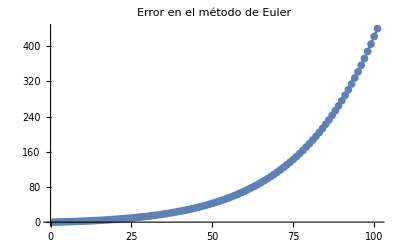

```mathematica
eulerG=ListLinePlot[eulerEr,
BaseStyle->texStyle,
PlotLabel->"Error en el método de Euler",
AxesLabel->(MaTeX[#,FontSize->16]&/@{"x","\\varepsilon"}),
Mesh->All]
```

```mathematica
Export[pwd<>"/plot-euler.pdf",eulerG]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/plot-euler.pdf

### Método de Taylor

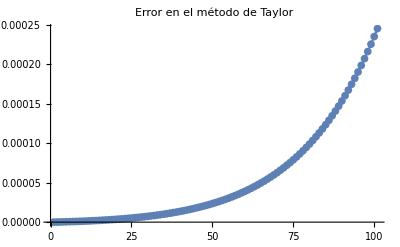

```mathematica
taylorG=ListLinePlot[taylorEr,
BaseStyle->texStyle,
PlotLabel->"Error en el método de Taylor",
AxesLabel->(MaTeX[#,FontSize->16]&/@{"x","\\varepsilon"}),
Mesh->All]
```

```mathematica
Export[pwd<>"/plot-taylor.pdf",taylorG]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/plot-taylor.pdf

### Método de Runge-Kutta

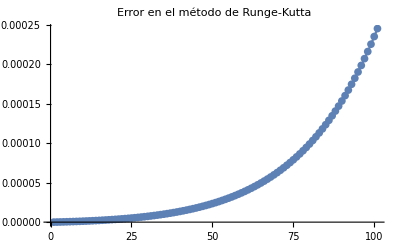

```mathematica
rungekuttaG=ListLinePlot[rungekuttaEr,
BaseStyle->texStyle,
PlotLabel->"Error en el método de Runge-Kutta",
AxesLabel->(MaTeX[#,FontSize->16]&/@{"x","\\varepsilon"}),
Mesh->All]
```

```mathematica
Export[pwd<>"/plot-runge_kutta.pdf",rungekuttaG]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/plot-runge_kutta.pdf

## Comparativa gráfica entre métodos

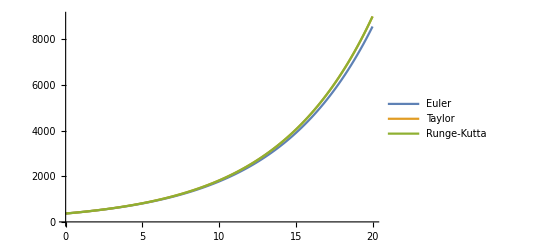

```mathematica
comp=ListLinePlot[{
euler[[;;,2;;]],
taylor[[;;,2;;]],
rungekutta[[;;,2;;]]
},
BaseStyle->texStyle,
AxesLabel->(MaTeX[#,FontSize->16]&/@{"x","y"}),
PlotLegends->Placed[LineLegend[{"Euler","Taylor","Runge-Kutta"},LegendFunction->Panel],{0.2,0.85}]
]
```

```mathematica
Export[pwd<>"/plot-comp.pdf",comp]
```

/Users/macbook/Desktop/Progra/Mathematica/Proyecto4LabSimu/plot-comp.pdf